Sensitivity Analysis on all input parameters (except universal constants)

## Setup

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social"];

(* Clear all variable names *)
Clear["Global`*"]
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Import / Construct Emissions Scenarios

```mathematica
(* Import historical emission data (goes up to year 2014) *)
historicalEmissionDataRaw=Import["export_data/historical_emissions.dat","Data"]//Transpose;
(* convert the years into timesteps - 1800 -> 0 *)
historicalEmissionData=historicalEmissionDataRaw-ConstantArray[{1800,0},Length[historicalEmissionDataRaw]];
(* make it a function of time *)
historicalEmissionFun=Interpolation[historicalEmissionData,InterpolationOrder->1];

(* Import RCP data *)
rcp2p6Raw=Import["export_data/rcp_data/rcp2p6.dat"];
rcp4p5Raw=Import["export_data/rcp_data/rcp4p5.dat"];
rcp6Raw=Import["export_data/rcp_data/rcp6.dat"];
rcp8p5Raw=Import["export_data/rcp_data/rcp8p5.dat"];
```

```mathematica
(* RCP emission trajecories (1800 - 2300) *)
rcp2p6=Interpolation[rcp2p6Raw-ConstantArray[{1800,0},Length[rcp2p6Raw]],InterpolationOrder->1];rcp4p5=Interpolation[rcp4p5Raw-ConstantArray[{1800,0},Length[rcp4p5Raw]],InterpolationOrder->1];rcp6=Interpolation[rcp6Raw-ConstantArray[{1800,0},Length[rcp6Raw]],InterpolationOrder->1];rcp8p5=Interpolation[rcp8p5Raw-ConstantArray[{1800,0},Length[rcp8p5Raw]],InterpolationOrder->1];
```

```mathematica
(* future trajectory used by Lenton (business as usual followed by linear decrease at 2200) *)
futureEmissionData1={{215,10.6},{220,11.4},{225,12.2},{250,14.5},{275,16.3},{300,20.3},{400,0},{1200,0}} ;
```

```mathematica
(* saturating emission function to use with social dynamics *)
s=50; (* half saturation time *)
linIncr=(11.3461-9.5093)/(214-205);
emax=s*linIncr;
Clear[satEmissionFun]
satEmissionFun[t_]:=((t-214) emax)/(t-214+s)+11.3461;
```

```mathematica
(* Lenton emission trajectory *)
emissionsLenton=Interpolation[Union[historicalEmissionData,futureEmissionData1],InterpolationOrder->1];
```

```mathematica
(* Saturating trajectory for use with social dyanmics *)
Clear[emissionsSoc]
emissionsSoc[t_]:=Which[t≤214,historicalEmissionFun[t],
t>214,satEmissionFun[t]];
```

```mathematica
(* Make plot of saturating emission function *)
timeTicks=Table[{100(i-1),1800+100(i-1)},{i,1,130}];
satEmissionPlotPre=Plot[emissionsSoc[t],{t,0,214},
PlotRange->All,
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"CO_2 Emissions (GtC yr^-1)",None},{"Year",None}}];
```

```mathematica
satEmissionPlotPost=Plot[emissionsSoc[t],{t,214,400},PlotStyle->Dashed];
```

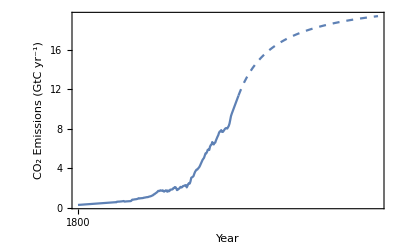

```mathematica
(* saturating energy plot *)
satEmissionPlot=Show[satEmissionPlotPre,satEmissionPlotPost]
```

```mathematica
(*Export["figures/emissionNosocialPlot.png",emissionNosocialPlot,ImageResolution->100];*)
```

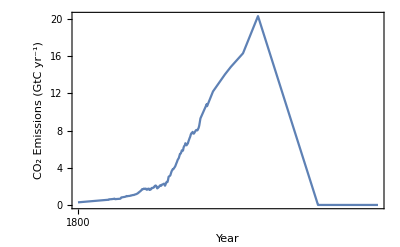

```mathematica
(* lenton emissions plot *)
emissionsLentonPlot=Plot[emissionsLenton[t],{t,0,500},
PlotRange->{All,All},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"CO_2 Emissions (GtC yr^-1)",None},{"Year",None}}]
```

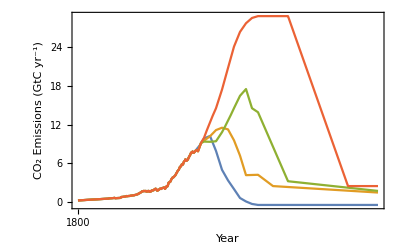

```mathematica
(* rcp emission plots *)
rcpEmissionPlot=Plot[{rcp2p6[t],rcp4p5[t],rcp6[t],rcp8p5[t]},{t,0,500},
PlotRange->{All,All},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"CO_2 Emissions (GtC yr^-1)",None},{"Year",None}}]
```

## Baseline Parameter Values along with lower and upper bounds

```mathematica
(* number of realisations *)
numSims=100;
```

### Parameter Labels

```mathematica
(* parameter labels *)
parLabels={"f_0","χ","ζ","x_0","κ","δ","β","f_max","ω","T_c","t_f","C_at0","C_oc0","C_ve0","C_so0","T_0","k_p","k_r","k_t","k_sr","k_c","k_M","E_a","k_MM","k_A","k_B","S","A","τ(CH_4)","P_0","c","s"};
numParams=Length[parLabels];
```

```mathematica
(* parameter definitions *)
parDefs={"Ocean flux rate constant","Characteristic CO_2 solubility","Evasion factor","Initial proportion of mitigators","Social learning rate","Strength of social norms","Cost to mitigate","Maximum of resopnse function","Curvature of response function","Threshold of response function","Time horizon of temperature projection","Pre-industrial CO_2 in atmosphere","Pre-industrial CO_2 in ocean","Pre-industrial CO_2 in vegetation","Pre-industrial CO_2 in soil","Pre-industrial temperature","Photosynthesis rate constant","Plant respiration constant","Turnover rate constant","Soil respiration rate constant","Photosynthesis compensation point","Half-saturation point","Plant respiration activation energy","Photosynthesis normalising constant","Plant respiration normalising constant","Soil respiration normalising constant","Solar flux","Surface albedo","Methane opacity","Water vapour saturation constant","Specific heat capacity of Earth's surface","Half-saturation time for ϵ(t)"};
```

```mathematica
(* parmaeter input codes *)
parCodes={"f0","chi","zeta","x0","κ","δ","β","fmax","omega","tempThresh","deltatFut","cat0","coc0","cve0","cso0","temp0","kp","kr","kt","ksr","kc","kM","ea","kMM","kA","kB","solar","albedo","tauch4","p0","cap","s"};
```

```mathematica
{Range[Length[parCodes]],parLabels}//Transpose//TableForm
```

1 | f_0
2 | χ
3 | ζ
4 | x_0
5 | κ
6 | δ
7 | β
8 | f_max
9 | ω
10 | T_c
11 | t_f
12 | C_at0
13 | C_oc0
14 | C_ve0
15 | C_so0
16 | T_0
17 | k_p
18 | k_r
19 | k_t
20 | k_sr
21 | k_c
22 | k_M
23 | E_a
24 | k_MM
25 | k_A
26 | k_B
27 | S
28 | A
29 | τ(CH_4)
30 | P_0
31 | c
32 | s

```mathematica
(* indexes of parameters that are subjected to triangular distributions *)
parIndexTri=Delete[Range[numParams],{{24},{25},{26}}];
```

### Choose emission scenario

```mathematica
(* Choose emission scenario from
emissionsLenton, emissionsSoc, rcp2p6, rcp4p6, rcp6, rcp8p5 *)
Clear[emissions]
emissions=emissionsSoc;
```

### Muryshev parameters

```mathematica
f0B=2.5*^-2; (* ocean flux constant (2.5-4.5 *10^-2) *)
{f0L,f0U}={0.9f0B,1.1f0B};
chiB=0.3; (* characterisitc co2 solubility in seawater (lower->higher temp anomaly) *)
{chiL,chiU}={0.2,0.4};
zetaB=50; (* buffer factor (higher-> reduces total carbon storage of ocean - long term temp higher *)
{zetaL,zetaU}={40,60};
```

### Social parameters

```mathematica
x0B=0.05; (* proportion of mitigators in 2010 *)
{x0L,x0U}={0.01,0.1};
κB=0.05; (* social learning rate *)
{κL,κU} = {0.02,0.2};
δB=1; (* strength of social norms *)
{δL,δU}={0.5,1.5};
βB=1.5; (* cost of adopting mitigatve strategies *)
{βL,βU}={0.5,1.5};
(* response function to temp *)
omegaB=3;
{omegaL,omegaU}={1,5};
tempThreshB=2.5;
{tempThreshL,tempThreshU}={2,3};
fmaxB=5;
{fmaxL,fmaxU}={4,6};
resType=1; (* 1 sigmoidal, 2 linear *)

(* temp prediction (linear extrapolation from previous temperatures) *) 
tempProjOnOff=1; (* on 1, off 0 *)
deltatPastB=10; (* based on previous number of years *)
deltatFutB=25; (* years looking ahead *)
{deltatFutL,deltatFutU}={0,50};

(* social adaptation on or off (1 for no social dynamics) *)
noSocial=0;
```

### Conversion factors

```mathematica
ka=1.773*^20; (* moles in atmosphere *)
gtcToMol=8.3259*^13;(* factor from gtC to moles *)
gtcToPpm=gtcToMol*10^6/ka; (* factor from gtc to ppmv *)
gtcTogtco2=3.664; (* factor from gtC from gtCO2 *)
secondstoyrs=60*60*24*365; (* factor from seconds to years *)
```

### Initial conditions (pre-industrial)

```mathematica
cat0B=596; (* initial carbon in the atmostphere *)
{cat0L,cat0U}={cat0B-6,cat0B+6};
coc0B=1.5*^5; (* initial carbon in the ocean *)
{coc0L,coc0U}={1.4*^5,1.6*^5};
cve0B=550; (* initial carbon in veg *)
{cve0L,cve0U}={cve0B-10,cve0B+10};
cso0B=1500; (*initical carbon in soil *)
{cso0L,cso0U}={cso0B-20,cso0B+20};
temp0B=288.15; 
{temp0L,temp0U}={288,288.3};(* inital temp *)
```

### Lenton parameters

```mathematica
kpB=0.184; (* photosyn rate *)
{kpL,kpU}={0.95*kpB,1.05*kpB};
krB=0.092; (*plant respiration rate *)
{krL,krU}={0.9*krB,1.1*krB};
ktB=0.092; (* turnover rate *)
{ktL,ktU}={0.9*ktB,1.1*ktB};
ksrB=0.0337; (* soil respiration rate *)
{ksrL,ksrU}={0.9*ksrB,1.1*ksrB};
kcB=29*^-6; (* compensation point *)
{kcL,kcU}={0.9*kcB,1.1*kcB};
kMB=120*^-6; (* half-saturation point - set to 145 for ocean warming *)
{kML,kMU}={0.9*kMB,1.1*kMB};
```

```mathematica
eaB=54830; (* plant respiration activation energy *)
{eaL,eaU}={54630,55030};
kMMB=1.478; (* photosyn normalising constnat - set to 1.578 for ocean warming *)
{kMML,kMMU}={0.9*kMMB,1.1*kMMB};
kAB=8.7039*^9; (* plant respiration normalising constant &*)
{kAL,kAU}={0.9*kAB,1.1*kAB};
kBB=157.072; (* soil respiration normalising constant*)
{kBL,kBU}={0.9*kBB,1.1*kBB};
solarB=1368; (* solar flux *)
{solarL,solarU}={0.9*solarB,1.1*solarB};
albedoB=0.225; (* surface albedo *)
{albedoL,albedoU}={0.9*albedoB,1.1*albedoB};
tauch4B=0.0231; (* methane opacity *)
{tauch4L,tauch4U}={0.9*tauch4B,1.1*tauch4B};
p0B=1.4*^11; (* water vapour saturation constant *)
{p0L,p0U}={0.9*p0B,1.1*p0B};
(* humidity parameter is fit to give pre-industrial steady state temperature of T=288.15K as in Lenton00 *)
capB=4.69*^23; (* specific heat capacity *)
{capL,capU}={0.9*capB,1.1*capB};
```

### Universal parameters

```mathematica
rgas=8.314; (* universal gas constant *)
lheat=43655; (* latent heat per mole of water *)
σ=5.67*^-8; (* Stefan-Boltzman constant*)
aE=5.101*^14; (* earth SA *)
```

### Emission parameter

```mathematica
sB=50; (* half saturation time of global energy demands *)
{sL,sU}={30,70};
```

## Create parameter distributions (Triangular)

### Function to take baseline parameter value to set of sampled values from tri distribution

```mathematica
triDev1=0.1; (* width of triangular distribution *)
triDev2=0.1; (* width of triangular distribution *)
```

```mathematica
(* p is baseline parameter value, σ is relative deviation from baseline value of edge of triangular distribution *)
Clear[triDist]
triDist[p_,σ_]:=RandomVariate[TriangularDistribution[{(1-σ)p,(1+σ)p},p],numSims]
```

```mathematica
(* create function that gives triangular distribution from specific upper and lower bounds *)
Clear[triDistLUB]
triDistLUB[{lower_,upper_,base_}]:=RandomVariate[TriangularDistribution[{lower,upper},base],numSims];
```

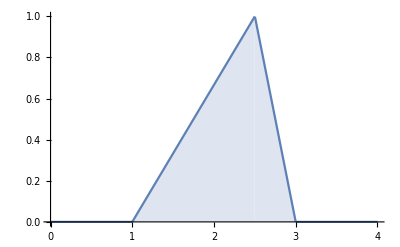

```mathematica
(* example *)
lower=1;upper=3;base=2.5;
Plot[PDF[TriangularDistribution[{lower,upper},base],x]//Evaluate,{x,0,4},Filling->Axis]
```

### Create Distributions for each parameter

```mathematica
(* create sample from triangle distribution for each parameter *)
parSamples=Table[triDistLUB[ToExpression[{parCodes[[i]] <> "L", parCodes[[i]] <> "U", parCodes[[i]] <> "B"}]],{i,parIndexTri}];
```

```mathematica
(* assign sample values to symbols for each parameter, e.g f0Tri. To assign again, variable names must be cleared *)
Evaluate[ToExpression[StringJoin[#,"Tri"]&/@parCodes[[parIndexTri]]]]=parSamples;
```

## Run system up to year 2014 with baseline param values

### Create Data Arrays for Storage

```mathematica
(* Initialise arrays for storage of data *)
catData=ConstantArray[0,numSims];
cocData=ConstantArray[0,numSims];
cveData=ConstantArray[0,numSims];
csoData=ConstantArray[0,numSims];
tempData=ConstantArray[0,numSims];
socData=ConstantArray[0,numSims];
emissionsData=ConstantArray[0,numSims];
```

### Assign baseline values

```mathematica
(* ocean *)
f0=f0B;
chi=chiB;
zeta=zetaB;

(* social *)
x0=x0B;
κ=κB;
δ=δB;
β=βB;
fmax=fmaxB;
omega=omegaB;
tempThresh=tempThreshB;

deltatPast=deltatPastB; (* based on previous number of years *)
deltatFut=deltatFutB; (* years looking ahead *)

(* initial carbon values *)
cat0=cat0B;
coc0=coc0B;
cve0=cve0B;
cso0=cso0B;
temp0=temp0B;

(* Lenton parameters *)
kp=kpB;
kr=krB;
kt=ktB;
ksr=ksrB;
kc=kcB;
kM=kMB;
ea=eaB;
kMM=kMMB;
kA=kAB;
kB=kBB;
solar=solarB;
albedo=albedoB;
tauch4=tauch4B;
p0=p0B;
cap=capB;

(* emission parameter *)
s=sB;
```

### Functional Forms

```mathematica
(* OCEAN DYNAMICS *)

(* carbon flux to ocean from atmosphere *)
Clear[foc];
foc[temp_,cat_,coc_]:=f0*chi*(cat-zeta*cat0*coc/coc0);

(* LAND DYNAMICS *)

(* atmospheric mixing ratio of co2 in atmosphere *)
Clear[pco2a];
pco2a[cat_]:=(cat+cat0)*gtcToMol/ka;
(* photosynthesis - from Lenton *)
Clear[photo]
photo[cat_,temp_]:=If[pco2a[cat]>kc&& -15<temp<25,
kp*cve0*kMM*((pco2a[cat]-kc)/(kM+pco2a[cat]-kc))*(((15+temp)^2)*(25-temp)/5625),
0];
(* respiration of plants *)
Clear[respp];
respp[temp_,cve_]:=kr*(cve+cve0)*kA*Exp[-(ea/(rgas*(temp+temp0)))];
(* turnover of plants *)
Clear[turnover];
turnover[cve_]:=kt*(cve+cve0);
(* respiration of soil *)
Clear[resps];
resps[temp_,cso_]:=ksr*(cso+cso0)*kB*Exp[-(308.56/(temp+temp0-227.13))];
(* carbon flux to land from atmosphere *)
Clear[fla];
fla[cat_,cve_,cso_,temp_]:=photo[cat,temp]-respp[temp,cve]-resps[temp,cso];

(* ATMOSPHERE DYANMICS *)

(* opacity of co2 *)
Clear[tauco2];
tauco2[ca_]:=1.73*pco2a[ca]^0.263;
(* opacity of h20 *)
Clear[hum];
Clear[tauh2o];
tauh2o[temp_,hum_]:=0.0126*(hum*p0*Exp[-lheat/(rgas*(temp+temp0))])^0.503;
(* total opacity *)
Clear[tau];
tau[ca_,temp_,hum_]:=tauco2[ca]+tauh2o[temp,hum]+tauch4;
(* downward flux of radiation *)
Clear[fd];
fd[ca_,temp_,hum_]:=((1-albedo)*solar/4)*(1+3tau[ca,temp,hum]/4);
(* Calibrate hum so that equilibirum temperature of 288.15K in 1800 *)
hum=humidity/.Quiet[Solve[fd[0,0,humidity]-σ temp0^4==0,humidity]][[1]];



(* SOCIAL DYNAMICS *)
(* social response to temperature function *)
Clear[resSig,resLin]
resSig[temp_]:=fmax/(1+Exp[-omega(temp-tempThresh)]);
resLin[temp_]:=fmax/5*temp;
(* assign response function *)
Clear[res]
Which[resType==1,res[temp_]:=resSig[temp],
resType==2,res[temp_]:=resLin[temp]];
```

### Run Dynamics

```mathematica
(* Clear variable names *)
Clear[cat,coc,cve,cso,temp,soc];

(* Run from t=0 to tcurrnet *)
tStep=0.1;
tcurrent=214; (* year 2020 *)
tmax=tcurrent;

(* Run evolution equations with baseline parameter values up to 2020 *)
sim1=NDSolve[{cat'[t]==emissions[t](1-soc[t])/(1-x0)-foc[temp[t],cat[t],coc[t]]-fla[cat[t],cve[t],cso[t],temp[t]],
coc'[t]==foc[temp[t],cat[t],coc[t]],
cve'[t]==photo[cat[t],temp[t]]-respp[temp[t],cve[t]]-turnover[cve[t]],
cso'[t]==turnover[cve[t]]-resps[temp[t],cso[t]],
temp'[t]==secondstoyrs*(aE/cap)*(fd[cat[t],temp[t],hum]-σ (temp[t]+temp0)^4),
soc'[t]==Which[0≤t≤tcurrent,0,
t>tcurrent && tempProjOnOff==1,κ*soc[t]*(1-soc[t])*(-β+res[temp[t]+(deltatFut/deltatPast)*(temp[t]-temp[t-deltatPast])]+(δ*(2soc[t]-1))),
t>tcurrent && tempProjOnOff==0,κ*soc[t]*(1-soc[t])*(-β+res[temp[t]]+(δ*(2soc[t]-1)))],
cat[t/;t≤0]==0,
coc[t/;t≤0]==0,
cve[t/;t≤0]==0,
cso[t/;t≤0]==0,
temp[t/;t≤0]==0,
soc[t/;t≤0]==x0},
{cat,coc,cve,cso,temp,soc},
{t,0,tmax}];

(* obtain series functions *)
Clear[catSeriesPre,cocSeriesPre,cveSeriesPre,csoSeriesPre,tempSeriesPre,socSeriesPre,emissionsSeriesPre];
catSeriesPre[t_]:=cat[t]/.sim1[[1]];
cocSeriesPre[t_]:=coc[t]/.sim1[[1]];
cveSeriesPre[t_]:=cve[t]/.sim1[[1]];
csoSeriesPre[t_]:=cso[t]/.sim1[[1]];
tempSeriesPre[t_]:=temp[t]/.sim1[[1]];
socSeriesPre[t_]:=soc[t]/.sim1[[1]];
emissionsSeriesPre[t_]:=emissions[t]*(1-socSeriesPre[t])/(1-x0);


(* Put into data form *)
catPreData=Table[catSeriesPre[t],{t,0,tmax,tStep}];
cocPreData=Table[cocSeriesPre[t],{t,0,tmax,tStep}];
cvePreData=Table[cveSeriesPre[t],{t,0,tmax,tStep}];
csoPreData=Table[csoSeriesPre[t],{t,0,tmax,tStep}];
tempPreData=Table[tempSeriesPre[t],{t,0,tmax,tStep}];
socPreData=Table[socSeriesPre[t],{t,0,tmax,tStep}];
emissionsPreData=Table[emissionsSeriesPre[t],{t,0,tmax,tStep}];
```

## For Loop over Parameter Values (comment out params not in sensitivity analysis)

### For Loop

```mathematica
For[i=1,i≤numSims,i++,

(* ASSIGN PARAMETER VALUES FROM TRIANGLE DISTRIBUTIONS *)

(* ocean *)
f0=f0Tri[[i]];
chi=chiTri[[i]];
zeta=zetaTri[[i]];

(* social *)
(*x0=x0Tri[[i]];*)
(*κ=κTri[[i]];*)
(*δ=δTri[[i]];*)
(*β=βTri[[i]];*)
fmax=fmaxTri[[i]];
omega=omegaTri[[i]];
tempThresh=tempThreshTri[[i]];
deltatPast=deltatPastB; (* based on previous number of years *)
deltatFut=deltatFutTri[[i]];

(* initial carbon values *)
cat0=cat0Tri[[i]];
coc0=coc0Tri[[i]];
cve0=cve0Tri[[i]];
cso0=cso0Tri[[i]];
temp0=temp0Tri[[i]];

(* Lenton parameters *)
kp=kpTri[[i]];
kr=krTri[[i]];
kt=ktTri[[i]];
ksr=ksrTri[[i]];
kc=kcTri[[i]];
kM=kMTri[[i]];
ea=eaTri[[i]];
(*kMM=kMMTri[[i]];
kA=kATri[[i]];
kB=kBTri[[i]];*)
solar=solarTri[[i]];
albedo=albedoTri[[i]];
tauch4=tauch4Tri[[i]];
p0=p0Tri[[i]];
cap=capTri[[i]];

(* emission parameter *)
(*s=sTri[[i]];*)



(* OCEAN DYNAMICS *)

(* carbon flux to ocean from atmosphere *)
Clear[foc];
foc[temp_,cat_,coc_]:=f0*chi*(cat-zeta*cat0*coc/coc0);

(* LAND DYNAMICS *)

(* atmospheric mixing ratio of co2 in atmosphere *)
Clear[pco2a];
pco2a[cat_]:=(cat+cat0)*gtcToMol/ka;
(* photosynthesis - from Lenton *)
Clear[photo];
photo[cat_,temp_]:=If[pco2a[cat]>kc&& -15<temp<25,
kp*cve0*kMM*((pco2a[cat]-kc)/(kM+pco2a[cat]-kc))*(((15+temp)^2)*(25-temp)/5625),
0];
(* respiration of plants *)
Clear[respp];
respp[temp_,cve_]:=kr*(cve+cve0)*kA*Exp[-(ea/(rgas*(temp+temp0)))];
(* turnover of plants *)
Clear[turnover];
turnover[cve_]:=kt*(cve+cve0);
(* respiration of soil *)
Clear[resps];
resps[temp_,cso_]:=ksr*(cso+cso0)*kB*Exp[-(308.56/(temp+temp0-227.13))];
(* carbon flux to land from atmosphere *)
Clear[fla];
fla[cat_,cve_,cso_,temp_]:=photo[cat,temp]-respp[temp,cve]-resps[temp,cso];

(* ATMOSPHERE DYANMICS *)

(* opacity of co2 *)
Clear[tauco2];
tauco2[ca_]:=1.73*pco2a[ca]^0.263;
(* opacity of h20 *)
Clear[hum];
Clear[tauh2o];
tauh2o[temp_,hum_]:=0.0126*(hum*p0*Exp[-lheat/(rgas*(temp+temp0))])^0.503;
(* total opacity *)
Clear[tau];
tau[ca_,temp_,hum_]:=tauco2[ca]+tauh2o[temp,hum]+tauch4;
(* downward flux of radiation *)
Clear[fd];
fd[ca_,temp_,hum_]:=((1-albedo)*solar/4)*(1+3tau[ca,temp,hum]/4);
(* Calibrate hum so that equilibirum temperature of 288.15K in 1800 *)
hum=humidity/.Quiet[Solve[fd[0,0,humidity]-σ temp0^4==0,humidity]][[1]];




(* SOCIAL DYNAMICS *)

(* social response to temperature function *)
Clear[resSig,resLin];
resSig[temp_]:=fmax/(1+Exp[-omega(temp-tempThresh)]);
resLin[temp_]:=fmax/5*temp;
(* assign response function *)
Clear[res];
Which[resType==1,res[temp_]:=resSig[temp],
resType==2,res[temp_]:=resLin[temp]];


(* RUN DYNAMICS *)

(* Clear variable names *)
Clear[cat,coc,cve,cso,temp,soc];

(* Max time *)
tmax=500;

(* Run evolution equations from t=tcurrent (=220) to t=tmax  *)
sim2=NDSolve[{cat'[t]==emissions[t](1-soc[t])/(1-x0)-foc[temp[t],cat[t],coc[t]]-fla[cat[t],cve[t],cso[t],temp[t]],
coc'[t]==foc[temp[t],cat[t],coc[t]],
cve'[t]==photo[cat[t],temp[t]]-respp[temp[t],cve[t]]-turnover[cve[t]],
cso'[t]==turnover[cve[t]]-resps[temp[t],cso[t]],
temp'[t]==secondstoyrs*(aE/cap)*(fd[cat[t],temp[t],hum]-σ (temp[t]+temp0)^4),
soc'[t]==Which[noSocial==1,0,
0≤t≤tcurrent,0,
t>tcurrent && tempProjOnOff==1,κ*soc[t]*(1-soc[t])*(-β+res[temp[t]+(deltatFut/deltatPast)*(temp[t]-temp[t-deltatPast])]+(δ*(2soc[t]-1))),
t>tcurrent && tempProjOnOff==0,κ*soc[t]*(1-soc[t])*(-β+res[temp[t]]+(δ*(2soc[t]-1)))],
cat[t/;t≤tcurrent]==catSeriesPre[t],
coc[t/;t≤tcurrent]==cocSeriesPre[t],
cve[t/;t≤tcurrent]==cveSeriesPre[t],
cso[t/;t≤tcurrent]==csoSeriesPre[t],
temp[t/;t≤tcurrent]==tempSeriesPre[t],
soc[t/;t≤tcurrent]==socSeriesPre[t]},
{cat,coc,cve,cso,temp,soc},
{t,tcurrent,tmax}];

(* obtain series functions *)
Clear[catSeries,cocSeries,cveSeries,csoSeries,tempSeries,socSeries,emissionSeries];
catSeries[t_]:=cat[t]/.sim2[[1]];
cocSeries[t_]:=coc[t]/.sim2[[1]];
cveSeries[t_]:=cve[t]/.sim2[[1]];
csoSeries[t_]:=cso[t]/.sim2[[1]];
tempSeries[t_]:=temp[t]/.sim2[[1]];
socSeries[t_]:=soc[t]/.sim2[[1]];
emissionSeries[t_]:=emissions[t]*(1-socSeries[t])/(1-x0);

(* Append arrays with data form post t=214 *)
catData[[i]]=Join[catPreData,Table[catSeries[t],{t,tcurrent+tStep,tmax,tStep}]];
cocData[[i]]=Join[cocPreData,Table[cocSeries[t],{t,tcurrent+tStep,tmax,tStep}]];
cveData[[i]]=Join[cvePreData,Table[cveSeries[t],{t,tcurrent+tStep,tmax,tStep}]];
csoData[[i]]=Join[csoPreData,Table[csoSeries[t],{t,tcurrent+tStep,tmax,tStep}]];
tempData[[i]]=Join[tempPreData,Table[tempSeries[t],{t,tcurrent+tStep,tmax,tStep}]];
socData[[i]]=Join[socPreData,Table[socSeries[t],{t,tcurrent+tStep,tmax,tStep}]];
emissionsData[[i]]=Join[emissionsPreData,Table[emissionSeries[t],{t,tcurrent+tStep,tmax,tStep}]];

]
```

## Analysis

```mathematica
tSeries=Range[0,tmax,tStep];
plRange={0,400};
(* time ticks *)
timeTicks=Table[{100(i-1),1800+100(i-1)},{i,1,130}];
```

### Compute Median, 5th and 95th Quantiles of the Post 2020 Dynamics

```mathematica
upperQuart=0.95;
lowerQuart=0.05;
midQuart=0.5;
```

```mathematica
{lowerCatSeries,medCatSeries,upperCatSeries}=Table[Quantile[catData[[;;,i]],{lowerQuart,midQuart,upperQuart}],{i,1,tmax/tStep+1}]//Transpose;

{lowerCocSeries,medCocSeries,upperCocSeries}=Table[Quantile[cocData[[;;,i]],{lowerQuart,midQuart,upperQuart}],{i,1,tmax/tStep+1}]//Transpose;

{lowerCveSeries,medCveSeries,upperCveSeries}=Table[Quantile[cveData[[;;,i]],{lowerQuart,midQuart,upperQuart}],{i,1,tmax/tStep+1}]//Transpose;

{lowerCsoSeries,medCsoSeries,upperCsoSeries}=Table[Quantile[csoData[[;;,i]],{lowerQuart,midQuart,upperQuart}],{i,1,tmax/tStep+1}]//Transpose;

{lowerTempSeries,medTempSeries,upperTempSeries}=Table[Quantile[tempData[[;;,i]],{lowerQuart,midQuart,upperQuart}],{i,1,tmax/tStep+1}]//Transpose;

{lowerSocSeries,medSocSeries,upperSocSeries}=Table[Quantile[socData[[;;,i]],{lowerQuart,midQuart,upperQuart}],{i,1,tmax/tStep+1}]//Transpose;

{lowerEmissionsSeries,medEmissionsSeries,upperEmissionsSeries}=Table[Quantile[emissionsData[[;;,i]],{lowerQuart,midQuart,upperQuart}],{i,1,tmax/tStep+1}]//Transpose;
```

### Make Error Plots

```mathematica
emissionSocialPlot=ListLinePlot[{Transpose[{tSeries,medEmissionsSeries}],
Transpose[{tSeries,lowerEmissionsSeries}],
Transpose[{tSeries,upperEmissionsSeries}]},
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5]},
Filling->{{2->{1}},{3->{1}}},
PlotRange->{plRange,{-0.5,20}},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"CO_2emissions (gtC yr^-1)",None},{"Year",None}}];
```

```mathematica
socPlot=ListLinePlot[{Transpose[{tSeries,medSocSeries}],
Transpose[{tSeries,lowerSocSeries}],
Transpose[{tSeries,upperSocSeries}]},
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5]},
Filling->{{2->{1}},{3->{1}}},
PlotRange->{plRange,{0,1}},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"Proportion mitigators",None},{"Year",None}}];
```

```mathematica
catPlot=ListLinePlot[{Transpose[{tSeries,medCatSeries}],
Transpose[{tSeries,lowerCatSeries}],
Transpose[{tSeries,upperCatSeries}]},
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5]},
Filling->{{2->{1}},{3->{1}}},
PlotRange->{plRange,All},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"Atmospheric CO_2 (ppmv)",None},{"Year",None}}];
```

```mathematica
tempPlot=ListLinePlot[{Transpose[{tSeries,medTempSeries}],
Transpose[{tSeries,lowerTempSeries}],
Transpose[{tSeries,upperTempSeries}]},
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5]},
Filling->{{2->{1}},{3->{1}}},
PlotRange->{plRange,All},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->400,
Frame->True,
LabelStyle->14,
FrameLabel->{{"Temperature change (K)",None},{"Year",None}}];
```

### Plot Grid

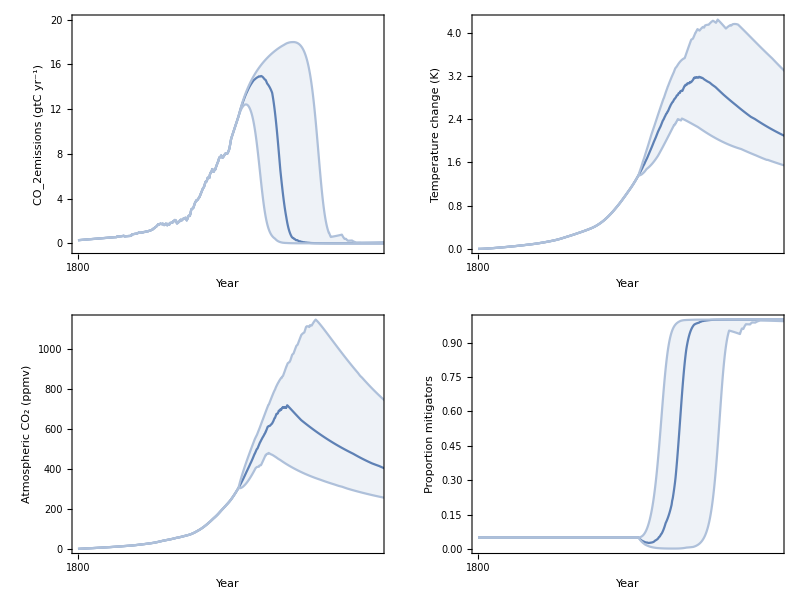

```mathematica
gridPlot=Grid[{{emissionSocialPlot,tempPlot},{catPlot,socPlot}}]
```

## Export Data

### Export all trajectories (high memory)

```mathematica
(*seriesData=Flatten[{socData,emissionsData,tempData},1];*)
```

```mathematica
(*Export["export_data/sensi_anal/delta_high2.dat",seriesData];*)
```

### Export summary statistics (low memory - better)

```mathematica
(* put together dataframe *)
(* {mitigators, co2 emissions, temp}, {timeVals, lower .05 percentile, median, upper percentile} *)
socialData = {tSeries,lowerSocSeries,medSocSeries,upperSocSeries};
emissionData = {tSeries,lowerEmissionsSeries,medEmissionsSeries,upperEmissionsSeries};
temData ={tSeries, lowerTempSeries,medTempSeries,upperTempSeries};
```

```mathematica
summaryData = {socialData,emissionData,temData};
```

```mathematica
(* export *)
Export["export_data/sensi_anal/beta_high.mat",summaryData];
```